### Metropolis sampling of a quarterly sales distribution

Set up the quarterly data. Define functions that make the quarter “to the left of” Q1 be Q4, and the quarter “to the right of” Q4 be Q1. Choose the initial position for the algorithm and normalize the sales.

```mathematica
unitSalesByQuarterInMillions={
{"Q1",25},
{"Q2",50},
{"Q3",100},
{"Q4",75}
};
annualUnitSales=Total[unitSalesByQuarterInMillions]⟦2⟧;
wrap[n_]:=Mod[n,4,1];
normalizedUnitSales=N[unitSalesByQuarterInMillions⟦All,2⟧/=annualUnitSales];
```

Implement the Metropolis algorithm.

```mathematica
(* Randomly walk one bin to the left or right of the current bin *)
proposedPosition[position_]:= wrap[position+(RandomInteger[{0,1}]*2-1)]
(* The acceptance ratio is determined by the probability distribution *)
acceptanceRatio[newPosition_, position_]:=normalizedUnitSales⟦newPosition⟧/(normalizedUnitSales⟦newPosition⟧+normalizedUnitSales⟦position⟧)

accumulate[l_]:=(
accumulator = l[[1]];
position = l[[2]];
(* Propose a new position *)
newPosition = proposedPosition[position];
(* Accept or reject the new position *)
ratio=acceptanceRatio[newPosition, position];position=If[RandomReal[]<ratio,newPosition,position];
(* Tally and return *)
accumulator⟦position⟧+=1;
{accumulator, position}
)
```

Use Nest[] to run accumulate a chosen number of iterations.

```mathematica
iterations=10000;
accumulator=ConstantArray[0,4];
initialPosition=RandomInteger[{1,4}];
Nest[accumulate,{accumulator, initialPosition},iterations];
```

Finally, plot what we accumulated (orange) next to the expected values from the original distribution (blue).

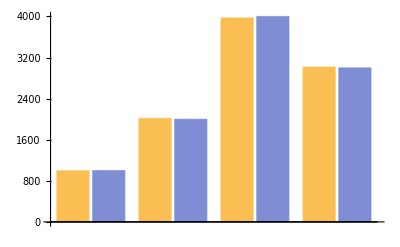

```mathematica
expected=normalizedUnitSales*iterations;
BarChart[Transpose[{accumulator,expected}]]
```